Clear::ssym: t_0 is not a symbol or a valid string pattern.

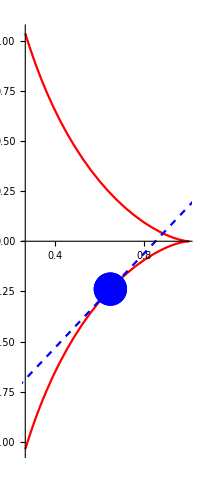

```mathematica
Clear[Subscript[t, 0]]
Subscript[t, 0]=-1;
Show[
ParametricPlot[{1/Cosh[u],u-Tanh[u]},{u,-2,2},PlotStyle->Red],
ListPlot[{{1/Cosh[Subscript[t, 0]],Subscript[t, 0]-Tanh[Subscript[t, 0]]}},PlotStyle->{Blue,PointSize[0.06]}],
ParametricPlot[{1/Cosh[Subscript[t, 0]]-λ Sinh[Subscript[t, 0]]/(Cosh[Subscript[t, 0]])^2,Subscript[t, 0]-Tanh[Subscript[t, 0]]+λ(1-1/(Cosh[Subscript[t, 0]])^2)},{λ,-2,2},PlotStyle->{Dashed,Blue}]
]
```

Clear::ssym: t_0 is not a symbol or a valid string pattern.

-4/3+u

256/81-(256 u)/27

1/2^(2/3)+u

1/(4 2^(2/3))+u

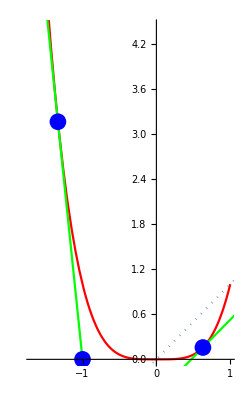

```mathematica
Clear[Subscript[t, 0]]
Subscript[t, 0]=-4/3;
Subscript[t, 1]=2^(-2/3);
Subscript[t, 0]+u
(Subscript[t, 0])^4+4u (Subscript[t, 0])^3
Subscript[t, 1]+u
(Subscript[t, 1])^4+4u (Subscript[t, 1])^3
Show[
ParametricPlot[{u,u^4},{u,-1.7,1},PlotStyle->Red],
ParametricPlot[{Subscript[t, 0]+u,(Subscript[t, 0])^4+4 u (Subscript[t, 0])^3},{u,-3,3},PlotStyle->Green],
ParametricPlot[{Subscript[t, 1]+u,(Subscript[t, 1])^4+4 u (Subscript[t, 1])^3},{u,-3,3},PlotStyle->Green],
Plot[x,{x,-10,10},PlotStyle->Dotted],
ListPlot[{{-1,0},{Subscript[t, 0],(Subscript[t, 0])^4},{Subscript[t, 1],(Subscript[t, 1])^4}},PlotStyle->{Blue,PointSize[0.03]}]
]
```

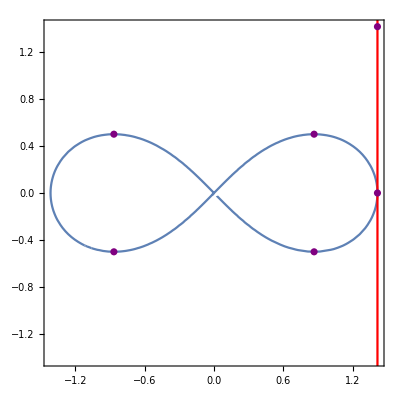

```mathematica
Show[
ContourPlot[(x^2+y^2)^2-2(x^2-y^2)==0,{x,-Sqrt[2],Sqrt[2]},{y,-Sqrt[2],Sqrt[2]}],
ContourPlot[x-Sqrt[2]==0,{x,-5,5},{y,-5,5},ContourStyle->Red],
ListPlot[{{Sqrt[2],0},{Sqrt[2],Sqrt[2]},{Sqrt[3]/2,1/2},{(-Sqrt[3])/2,1/2},{Sqrt[3]/2,-1/2},{(-Sqrt[3])/2,-1/2}},PlotStyle->Purple]
]
```

```mathematica
Solve[Subscript[x, 0]((Subscript[x, 0])^2+(Subscript[y, 0])^2-1)(Sqrt[2]-Subscript[x, 0])+Subscript[y, 0]((Subscript[x, 0])^2+(Subscript[y, 0])^2-1)(Sqrt[2]-Subscript[y, 0])==0&&((Subscript[x, 0])^2+(Subscript[y, 0])^2)^2-2((Subscript[x, 0])^2-(Subscript[y, 0])^2)==0,{Subscript[x, 0],Subscript[y, 0]}]
```

{{x_0→0,y_0→0},{x_0→√2,y_0→0},{x_0→-(√3)/2,y_0→-1/2},{x_0→-(√3)/2,y_0→1/2},{x_0→(√3)/2,y_0→-1/2},{x_0→(√3)/2,y_0→1/2}}

```mathematica
Integrate[a Sqrt[1+(Sinh[t])^2],{t,-C,C},Assumptions->Im[C]==0]
```

2 a Sinh[C]